λs_u=V*_(su)V_ub
λs_t=V_(st)V*_tb

```mathematica
A=0.826 ;(*PDG*)
λ=0.225 ;(*PDG*)
bρ=0.159;
bη=0.348;
ρ=bρ/(1-λ^2/2);
η=bη/(1-λ^2/2);
Vus=0.22;
Vub=A λ^3(ρ-I η);
Vts=-A λ^2;
Vtb=1;
Subscript[λ, u]= Vub Vus*
Subscript[λ, t]=Vtb Vts*
Clear[λ];
```

0.000337662-0.000739034 ⅈ

-0.0418163

## Phenomeology

```mathematica
Clear[ma]
```

```mathematica
Subscript[α, s]=0.21;(* at μ=5 GeV. Value from PDG plot*)
Subscript[λ, u]=Vub Vus*;(*values calculated from PDG*)
Subscript[λ, t]=Vtb Vts* ;(*values calculated from PDG*)
Subscript[c, 1]=1.082; (*NLO Table 1 QCD Fact B to pi K *)
Subscript[c, 2]=-0.191;
Subscript[c, 3]=0.013;
Subscript[c, 4]=-0.036;
Subscript[c, 8]=0.0126;
nc=3;
fk=0.160;(*GeV*)(*Table 2 QCD Fact B to pi K*)
fb=0.194;(*GeV*)(*PhD thesis*)
mb=5.279;(*GeV*)
ms=0.0934;(*GeV*)
Subscript[μ, k]=2.55;(*GeV ((0.493.b2)/(0.093+0.002))*)
mk=0.493;(*GeV by PDG*)
r=ma^2/mb^2;
Subscript[ω, o]=0.460;(*GeV at 1GeV*)
Gf=1.166×10^(-5);(*GeV^-2*)
l[r_]:=(r^2-2r Log[r]-1)/(r-1)^3;
τB= 2.489 10^(12);(*GeV^-1*)
a =Gf/Sqrt[2](Subscript[λ, u](nc Subscript[c, 1]+Subscript[c, 2])-Subscript[λ, t](nc Subscript[c, 4]+Subscript[c, 3]))/nc(fk fb)((mb^2-ma^2)/2)((κb-κS)/f);
b=-Subscript[λ, t] Gf/Sqrt[2] Subscript[c, 8](Subscript[α, s]/π)((nc^2-1)/(2nc^2))(fk fb)/4( mb^2 ((κS-κB)/f)(Subscript[μ, k]/Subscript[ω, o])+3mb^2((2κS-κB-κb)/f)+3 ma^2((κb-κB)/f)+3(mb^2-ma^2)(ms/Subscript[ω, o])((κs-κS)/f)l[r]);
d=-Subscript[λ, t] Gf/Sqrt[2] Subscript[c, 8](Subscript[α, s]/π)((nc^2-1)/(2nc^2))(fk fb)/4(Cg/f)(Subscript[α, s]/Pi)mb^3/Subscript[ω, o](mb^2-ma^2)l[r];
λ[u_,v_]=1-2(u+v)+(u-v)^2;
Decay[x_]= Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]/(16Pi mb)Abs[x]^2;
Clear[f]
```

Biggest contribution A

```mathematica
Abs[Gf/Sqrt[2](Subscript[λ, u](nc Subscript[c, 1]+Subscript[c, 2])-Subscript[λ, t](nc Subscript[c, 4]+Subscript[c, 3]))/nc(fk fb)((mb^2-ma^2)/2)]/.ma->0
```

4.40716×10^-9

```mathematica
Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]/(16Pi mb)Abs[a]^2/.ma->0//Simplify
```

7.2559×10^-20 Abs[(κb-κS)/f]^2

```mathematica
Decay[a]τB/.ma->0
```

1.80599×10^-7 Abs[(κb-κS)/f]^2

```mathematica
NSolve[1.8 10^(-7) x^2==2.3 10^(-5),x]
```

{{x→-11.3039},{x→11.3039}}

Massless case (ma->0)

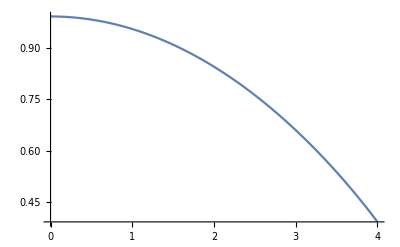

```mathematica
ListCouplings={κS,κB,κb,κs,Cg};
AκS=Limit[Abs[a+b+d],ma->0]/.κS->1/.Thread[ListCouplings:> 0];
(**Coef for κS*)
(*Aκs=Limit[Abs[a+b+d],ma->0]/.κs->1/.Thread[ListCouplings:> 0];Aκs κs(*Coef for κs*)
AκB=Limit[Abs[a+b+d],ma->0]/.κB->1/.Thread[ListCouplings:> 0];AκB κB(*Coef for κB*)
Aκb=Limit[Abs[a+b+d],ma->0]/.κb->1/.Thread[ListCouplings:> 0];Aκb κb(*Coef for κb*)
Acg=Limit[Abs[a+b+d],ma->0]/.Cg->1/.Thread[ListCouplings:> 0];Acg Cg(*Coef for Cg*)*)
```

```mathematica
AκS κS
```

4.65294×10^-12 κS

```mathematica
(AκS κS)/(Gf mb fk fb)(**Coef for κS*)
```

2.43532×10^-6 κS

```mathematica
BRS=(AκS κS)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->0
BRs=(Aκs κs)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->0
BRB=(AκB κB)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->0
BRb=(Aκb κb)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->0
BRg=(Acg Cg)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->0
DκS=Limit[Decay[a+b+d]τB,ma->0]/.κS->1/.Thread[ListCouplings:> 0];DκS κS^2
```

2.01304×10^-13 κS^2

2.68734×10^-18 κs^2

5.28653×10^-16 κB^2

1.86108×10^-13 κb^2

3.31005×10^-15 Cg^2

2.01304×10^-13 κS^2

```mathematica
BRexp=2.3 10^(-5);
BRexpErr = Sqrt[0.5^2+0.5^2]10^(-5);
BRtheoErr=0;
```

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRS)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κSavg=NSolve[Chi2==0,κS][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κSmin=NSolve[Chi2-ChiMin==1,κS][[3,All,2]];(* min value given by 1σ*)
κSmax=NSolve[Chi2-ChiMin==1,κS][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κS]
κSavg
κSmax-κSavg
κSavg-κSmin
Plot[{Chi2,1},{κS,0,1.5 10^4}];
```

{{κS→-12222.2},{κS→-8895.42},{κS→8895.42},{κS→12222.2}}

{10689.}

{1533.15}

{1793.58}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRs)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κsavg=NSolve[Chi2==0,κs][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κsmin=NSolve[Chi2-ChiMin==1,κs][[3,All,2]];(* min value given by 1σ*)
κsmax=NSolve[Chi2-ChiMin==1,κs][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κs]
κsavg
κsmax-κsavg
κsavg-κsmin
Plot[{Chi2,1},{κs,0,5 10^6}];
```

{{κs→-3.34513×10^6},{κs→-2.43463×10^6},{κs→2.43463×10^6},{κs→3.34513×10^6}}

{2.92552×10^6}

{419614.}

{490893.}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRB)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κBavg=NSolve[Chi2==0,κB][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κBmin=NSolve[Chi2-ChiMin==1,κB][[3,All,2]];(* min value given by 1σ*)
κBmax=NSolve[Chi2-ChiMin==1,κB][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κB]
κBavg
κBmax-κBavg
κBavg-κBmin
Plot[{Chi2,1},{κB,0,3 10^5}];
```

{{κB→-238500.},{κB→-173583.},{κB→173583.},{κB→238500.}}

{208583.}

{29917.5}

{34999.5}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRb)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κbavg=NSolve[Chi2==0,κb][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κbmin=NSolve[Chi2-ChiMin==1,κb][[3,All,2]];(* min value given by 1σ*)
κbmax=NSolve[Chi2-ChiMin==1,κb][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κb]
κbavg
κbmax-κbavg
κbavg-κbmin
Plot[{Chi2,1},{κb,0,3 10^5}];
```

{{κb→-12711.4},{κb→-9251.48},{κb→9251.48},{κb→12711.4}}

{11116.8}

{1594.52}

{1865.37}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRg)^2/(BRexpErr^2+BRtheoErr^2)
ChiMin=0;
Cgavg=NSolve[Chi2==0,Cg][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
Cgmin=NSolve[Chi2-ChiMin==1,Cg][[3,All,2]];(* min value given by 1σ*)
Cgmax=NSolve[Chi2-ChiMin==1,Cg][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,Cg]
Cgavg
Cgmax-Cgavg
Cgavg-Cgmin
Plot[{Chi2,1},{Cg,0, 1.2 10^5}];
```

2.×10^10 (0.000023-3.31005×10^-15 Cg^2)^2

{{Cg→-95314.1},{Cg→-69370.7},{Cg→69370.7},{Cg→95314.1}}

{83357.9}

{11956.2}

{13987.2}

Light ALP case (ma->1 GeV)

```mathematica
Clear[κS,κs,κB,κb,Cg];
Clear[AκS,Aκs,AκB,Aκb,Acg]
ListCouplings={κS,κB,κb,κs,Cg};
AκS=Limit[Abs[a+b+d],ma->1]/.κS->1/.Thread[ListCouplings:> 0];AκS κS(**Coef for κS*)
Aκs=Limit[Abs[a+b+d],ma->1]/.κs->1/.Thread[ListCouplings:> 0];Aκs κs(*Coef for κs*)
AκB=Limit[Abs[a+b+d],ma->1]/.κB->1/.Thread[ListCouplings:> 0];AκB κB(*Coef for κB*)
Aκb=Limit[Abs[a+b+d],ma->1]/.κb->1/.Thread[ListCouplings:> 0];Aκb κb(*Coef for κb*)
Acg=Limit[Abs[a+b+d],ma->1]/.Cg->1/.Thread[ListCouplings:> 0] ; Acg Cg (*Coeff for Cg*)
```

4.49746×10^-12 κS

1.38984×10^-14 κs

2.41448×10^-13 κB

4.31332×10^-12 κb

4.87776×10^-13 Cg

```mathematica
Clear[BRS,BRs,BRB,BRb,BRg]
BRS=(AκS κS)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->1
BRs=(Aκs κs)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->1
BRB=(AκB κB)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->1
BRb=(Aκb κb)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->1
BRg=(Acg Cg)^2/(16Pi mb) Sqrt[λ[mk^2/mb^2,ma^2/mb^2]]τB/.ma->1
```

1.81144×10^-13 κS^2

1.72988×10^-18 κs^2

5.22079×10^-16 κB^2

1.66614×10^-13 κb^2

2.13073×10^-15 Cg^2

```mathematica
BRexp=2.3 10^(-5);
BRexpErr = Sqrt[0.5^2+0.5^2]10^(-5);
BRtheoErr=0;
```

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRS)^2/(BRexpErr^2+BRtheoErr^2)
ChiMin=0;
κSavg=NSolve[Chi2==0,κS][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κSmin=NSolve[Chi2-ChiMin==1,κS][[3,All,2]];(* min value given by 1σ*)
κSmax=NSolve[Chi2-ChiMin==1,κS][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κS]
κSavg
κSmax-κSavg
κSavg-κSmin
Plot[{Chi2,1},{κS,0, 1.2 10^5}];
```

2.×10^10 (0.000023-1.81144×10^-13 κS^2)^2

{{κS→-12884.4},{κS→-9377.39},{κS→9377.39},{κS→12884.4}}

{11268.1}

{1616.22}

{1890.76}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRs)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κsavg=NSolve[Chi2==0,κs][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κsmin=NSolve[Chi2-ChiMin==1,κs][[3,All,2]];(* min value given by 1σ*)
κsmax=NSolve[Chi2-ChiMin==1,κs][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κs]
κsavg
κsmax-κsavg
κsavg-κsmin
Plot[{Chi2,1},{κs,0,5 10^6}];
```

{{κs→-4.16933×10^6},{κs→-3.03449×10^6},{κs→3.03449×10^6},{κs→4.16933×10^6}}

{3.64633×10^6}

{523002.}

{611842.}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRB)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κBavg=NSolve[Chi2==0,κB][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κBmin=NSolve[Chi2-ChiMin==1,κB][[3,All,2]];(* min value given by 1σ*)
κBmax=NSolve[Chi2-ChiMin==1,κB][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κB]
κBavg
κBmax-κBavg
κBavg-κBmin
Plot[{Chi2,1},{κB,0,3 10^5}];
```

{{κB→-239997.},{κB→-174673.},{κB→174673.},{κB→239997.}}

{209892.}

{30105.3}

{35219.2}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRb)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κbavg=NSolve[Chi2==0,κb][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κbmin=NSolve[Chi2-ChiMin==1,κb][[3,All,2]];(* min value given by 1σ*)
κbmax=NSolve[Chi2-ChiMin==1,κb][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κb]
κbavg
κbmax-κbavg
κbavg-κbmin
Plot[{Chi2,1},{κb,0,3 10^5}];
```

{{κb→-13434.4},{κb→-9777.71},{κb→9777.71},{κb→13434.4}}

{11749.2}

{1685.21}

{1971.47}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRg)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
Cgavg=NSolve[Chi2==0,Cg][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
Cgmin=NSolve[Chi2-ChiMin==1,Cg][[3,All,2]];(* min value given by 1σ*)
Cgmax=NSolve[Chi2-ChiMin==1,Cg][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,Cg]
Cgavg
Cgmax-Cgavg
Cgavg-Cgmin
Plot[{Chi2,1},{Cg,0, 1.2 10^5}];
```

{{Cg→-118798.},{Cg→-86462.8},{Cg→86462.8},{Cg→118798.}}

{103896.}

{14902.1}

{17433.4}

Light ALP case (ma->4 GeV)

```mathematica
DS=Limit[Decay[a+b+d]τB,ma->4]/.κS->1/.Thread[ListCouplings:> 0];DS κS^2
Ds=Limit[Decay[a+b+d]τB,ma->4]/.κs->1/.Thread[ListCouplings:> 0];Ds κs^2
DB=Limit[Decay[a+b+d]τB,ma->4]/.κB->1/.Thread[ListCouplings:> 0];DB κB^2
Db=Limit[Decay[a+b+d]τB,ma->4]/.κb->1/.Thread[ListCouplings:> 0];Db κb^2
Dg=Limit[Decay[a+b+d]τB,ma->4]/.Cg->1/.Thread[ListCouplings:> 0];Dg Cg^2
```

1.68367×10^-14 κS^2

3.56577×10^-20 κs^2

3.02153×10^-16 κB^2

1.33608×10^-14 κb^2

4.39204×10^-17 Cg^2

```mathematica
BRexp=2.3 10^(-5);
BRexpErr = Sqrt[0.5^2+0.5^2]10^(-5);
BRtheoErr=0;
```

```mathematica
Clear[Chi2];
Clear[κSmax,κSmin,κSavg,κS];
Chi2= ((BRexp - DS κS^2)^2)/(BRexpErr^2+BRtheoErr^2)
ChiMin=0;
κSavg=NSolve[Chi2==0,κS][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κSmin=NSolve[Chi2-ChiMin==1,κS][[3,All,2]];(* min value given by 1σ*)
κSmax=NSolve[Chi2-ChiMin==1,κS][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κS]
κSavg
κSmax-κSavg
κSavg-κSmin
Plot[{Chi2,1},{κS,0, 1.2 10^5}];
```

2.×10^10 (0.000023-1.68367×10^-14 κS^2)^2

{{κS→-42261.6},{κS→-30758.5},{κS→30758.5},{κS→42261.6}}

{36960.3}

{5301.31}

{6201.82}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRs)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κsavg=NSolve[Chi2==0,κs][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κsmin=NSolve[Chi2-ChiMin==1,κs][[3,All,2]];(* min value given by 1σ*)
κsmax=NSolve[Chi2-ChiMin==1,κs][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κs]
κsavg
κsmax-κsavg
κsavg-κsmin
Plot[{Chi2,1},{κs,0,5 10^6}];
```

{{κs→-4.16933×10^6},{κs→-3.03449×10^6},{κs→3.03449×10^6},{κs→4.16933×10^6}}

{3.64633×10^6}

{523002.}

{611842.}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRB)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κBavg=NSolve[Chi2==0,κB][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κBmin=NSolve[Chi2-ChiMin==1,κB][[3,All,2]];(* min value given by 1σ*)
κBmax=NSolve[Chi2-ChiMin==1,κB][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κB]
κBavg
κBmax-κBavg
κBavg-κBmin
Plot[{Chi2,1},{κB,0,3 10^5}];
```

{{κB→-239997.},{κB→-174673.},{κB→174673.},{κB→239997.}}

{209892.}

{30105.3}

{35219.2}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRb)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
κbavg=NSolve[Chi2==0,κb][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
κbmin=NSolve[Chi2-ChiMin==1,κb][[3,All,2]];(* min value given by 1σ*)
κbmax=NSolve[Chi2-ChiMin==1,κb][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,κb]
κbavg
κbmax-κbavg
κbavg-κbmin
Plot[{Chi2,1},{κb,0,3 10^5}];
```

{{κb→-13434.4},{κb→-9777.71},{κb→9777.71},{κb→13434.4}}

{11749.2}

{1685.21}

{1971.47}

```mathematica
Clear[Chi2];
Chi2= (BRexp - BRg)^2/(BRexpErr^2+BRtheoErr^2);
ChiMin=0;
Cgavg=NSolve[Chi2==0,Cg][[3,All,2]];(*Since the minimum value of Chi2 is zero we can find the fitting solving chi2=0*)
Cgmin=NSolve[Chi2-ChiMin==1,Cg][[3,All,2]];(* min value given by 1σ*)
Cgmax=NSolve[Chi2-ChiMin==1,Cg][[4,All,2]];(* max value given by 1σ*)
NSolve[Chi2-ChiMin==1,Cg]
Cgavg
Cgmax-Cgavg
Cgavg-Cgmin
Plot[{Chi2,1},{Cg,0, 1.2 10^5}];
```

{{Cg→-118798.},{Cg→-86462.8},{Cg→86462.8},{Cg→118798.}}

{103896.}

{14902.1}

{17433.4}

Biggest Contribution

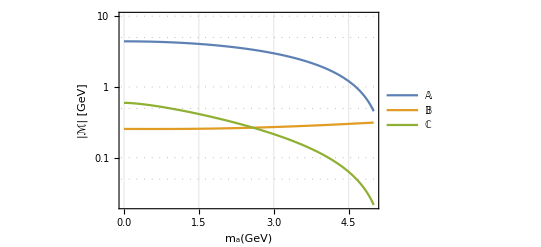

```mathematica
LogPlot[{Abs[a] 10^(9)/.(κb-κS)/f->1 ,Abs[b]10^9/.(κS-κB)/f->1/.(κb-κB)/f->1/.(-κb-κB+2κS)/f->1 /.(κs-κS)/f->1,Abs[d]10^9/.Cg/f->1},{ma,0,5},PlotRange->{0,10},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],"|ℳ| [GeV]"},Frame->True,Axes->True,PlotLegends->{"𝔸","𝔹","ℂ"}]
```

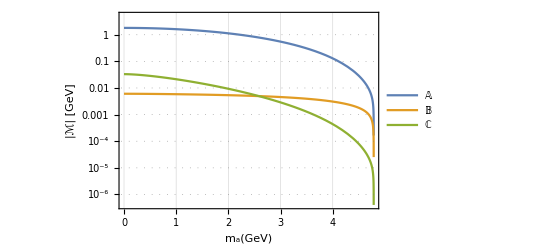

```mathematica
LogPlot[{Decay[a] τB 10^7/.(κb-κS)/f->1 ,Decay[b] τB 10^7/.(κS-κB)/f->1/.(κb-κB)/f->1/.(-κb-κB+2κS)/f->1 /.(κs-κS)/f->1,Decay[d]τB 10^7/.Cg/f->1},{ma,0,5},PlotRange->{0,5},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],"|ℳ| [GeV]"},Frame->True,Axes->True,PlotLegends->{"𝔸","𝔹","ℂ"}]
```

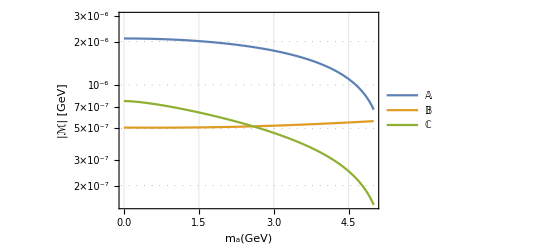

```mathematica
LogPlot[{Sqrt[Abs[a]] /.κb-κS->1 ,Sqrt[Abs[b]]/.κS-κB->1/.κb-κB->1/.-κb-κB+2κS->1 /.κs-κS->1,Sqrt[Abs[d]]/.Cg->1},{ma,0,5},PlotRange->{0, 3 10^-6},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],"|ℳ|  [GeV]"},Frame->True,Axes->True,PlotLegends->{"𝔸","𝔹","ℂ"}]
```

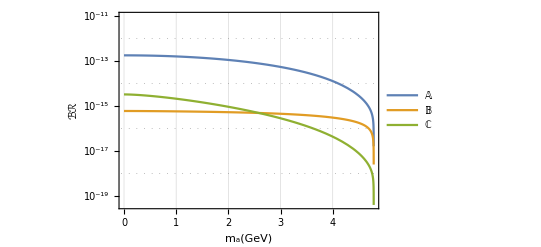

```mathematica
LogPlot[{Decay[a] τB/.κb-κS->1 ,Decay[b]τB/.κS-κB->1/.κb-κB->1/.-κb-κB+2κS->1 /.κs-κS->1,Decay[d]τB/.Cg->1},{ma,0,5},PlotRange->{0, 10^-11},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],ℬℛ},Frame->True,Axes->True,PlotLegends->{"𝔸","𝔹","ℂ"}]
```

```mathematica
Decay[a] 10^25/.κb-κS->1 /.ma->0
```

0.72559

Dependency of the Γ for each ALP-coupling on the ALP mass

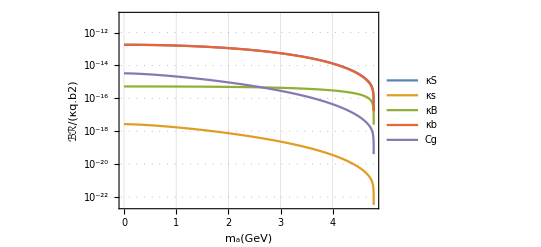

```mathematica
ListCouplings={κS,κB,κb,κs,Cg};
LogPlot[{(Decay[a]+Decay[b]+Decay[d]) τB/. κS->1/.Thread[ListCouplings:>0],(Decay[a]+Decay[b]+Decay[d]) τB/. κs->1/.Thread[ListCouplings:>0],(Decay[a]+Decay[b]+Decay[d]) τB/. κB->1/.Thread[ListCouplings:>0],(Decay[a]+Decay[b]+Decay[d]) τB/. κb->1/.Thread[ListCouplings:>0],
(Decay[a]+Decay[b]+Decay[d]) τB/. Cg->1/.Thread[ListCouplings:>0]},{ma,0,5},PlotRange->{0, 10^-11},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],ℬℛ/(κq.b2)},Frame->True,Axes->True,PlotLegends->{"κS","κs","κB","κb","Cg"}]
```

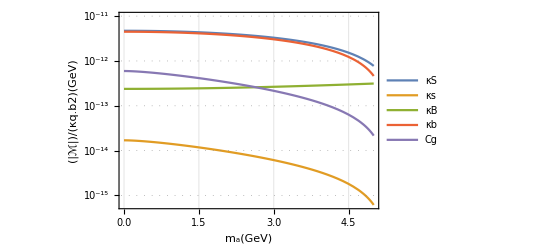

```mathematica
ListCouplings={κS,κB,κb,κs,Cg};
LogPlot[{(Abs[a]+Abs[b]+Abs[d]) /. κS->1/.Thread[ListCouplings:>0],(Abs[a]+Abs[b]+Abs[d])/. κs->1/.Thread[ListCouplings:>0],(Abs[a]+Abs[b]+Abs[d]) /. κB->1/.Thread[ListCouplings:>0],(Abs[a]+Abs[b]+Abs[d]) /. κb->1/.Thread[ListCouplings:>0],
(Abs[a]+Abs[b]+Abs[d]) /. Cg->1/.Thread[ListCouplings:>0]},{ma,0,5},PlotRange->{0, 10^-11},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],(("|ℳ|")/(κq.b2))[GeV]},Frame->True,Axes->True,PlotLegends->{"κS","κs","κB","κb","Cg"}]
```

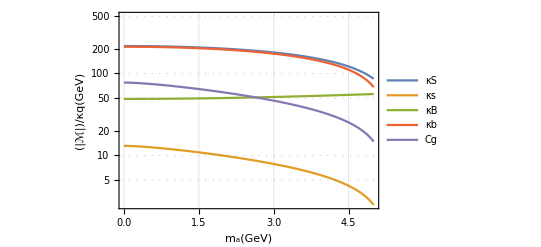

```mathematica
ListCouplings={κS,κB,κb,κs,Cg};
LogPlot[{(Sqrt[Abs[a+b+d]]) 10^8 /. κS->1/.Thread[ListCouplings:>0],(Sqrt[Abs[a+b+d]])10^8/. κs->1/.Thread[ListCouplings:>0],(Sqrt[Abs[a+b+d]]) 10^8/. κB->1/.Thread[ListCouplings:>0],Sqrt[Abs[a+b+d]]10^8 /. κb->1/.Thread[ListCouplings:>0],Sqrt[Abs[a+b+d]]10^8 /. Cg->1/.Thread[ListCouplings:>0]},{ma,0,5},PlotRange->{0, 500 },GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],(("|ℳ|")/κq)[GeV]},Frame->True,Axes->True,PlotLegends->{"κS","κs","κB","κb","Cg"}]
```

```mathematica
Series[(Decay[a]+Decay[b]+Decay[d]) τB/. κS->1/.Thread[ListCouplings:>0],{ma,0,2}]//Simplify;
```

1/θ^2 2.489×10^12 √(0.982633-0.0723932 ma^2+0.00128764 ma^4) (9.42516×10^-29 Abs[(-27.8678+ma^2) θ]^2+3.77985×10^-27 Abs[(θ (236.648-14.7815 ma^2+0.338667 ma^4-0.946122 ma^2 Log[ma^2]))/(-27.8678+ma^2)^2]^2)

2.489×10^12 (0.+9.42516×10^-29 √(1+(0.00872149-0.0358837 ma^2)^2-2 (0.00872149+0.0358837 ma^2)) Abs[-27.8678+ma^2]^2+3.77985×10^-27 √(1+(0.00872149-0.0358837 ma^2)^2-2 (0.00872149+0.0358837 ma^2)) Abs[0.321692-(0.00060913 (27.8678-ma^2) (-1+0.00128764 ma^4-0.0717673 ma^2 Log[0.0358837 ma^2]))/(-1+0.0358837 ma^2)^3]^2)

```mathematica
$Assumptions=ma<5;
Series[(Decay[a]+Decay[b]+Decay[d]) τB/. κS->1/.Thread[ListCouplings:>0],{ma,0,2}]//Simplify
```

Abs[236.648-14.7815 ma^2+0.338667 ma^4-0.946122 ma^2 Log[ma^2]]^2 (1.54626×10^-20+1.64983×10^-21 ma^2+O[ma]^3)+(1.80599×10^-13-1.96138×10^-14 ma^2+O[ma]^3)

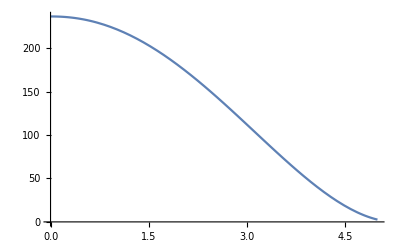

```mathematica
Plot[236.648-14.781518476617235 ma^2+ 0.3386669668656522 ma^4- 0.9461215681424302 ma^2 Log[ma^2],{ma,0,5}]
```

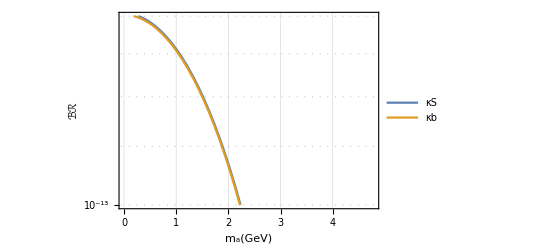

```mathematica
LogPlot[{(Decay[a]+Decay[b]+Decay[d]) τB/. κS->1/.Thread[ListCouplings:>0],(Decay[a]+Decay[b]+Decay[d]) τB/. κb->1/.Thread[ListCouplings:>0]},{ma,0,5},PlotRange->{10^-13, 1.8 10^-13},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted],FrameLabel->{"m_a"[GeV],ℬℛ},Frame->True,Axes->True,PlotLegends->{"κS","κb"}]
```